# Homework assignment 6

Kyle McGraw <kmcgraw@caltech.edu>, Collaborated with Dallas Taylor

## Part 2: Chemostatting the Srinivas et al oscillator.

This exercise aims to understand the CRN-to-DSD compilation for the rock-paper-scissors oscillator, and to demonstrate its performance when fuel and waste molecules are chemostatted.

(a) Informally compare the behavior of the simplified DSD rock-paper-scissors oscillator (using the Srinivas et al scheme) to the behavior of the 3-reaction abstract CRN.  Comment on time scales, asymptotic behavior, etc.

```mathematica
Vm=50;  (* volume is V * 1.66 fL when using nM in rate constants *)
CyclicPredatorPrey={
rxninstance[R+P,2P,1/Vm],
rxninstance[P+S,2S,1/Vm],
rxninstance[S+R,2R,1/Vm]
};
```

```mathematica
schemataCPP=CyclicPredatorPrey
```

{rxninstance[P+R,2 P,1/50],rxninstance[P+S,2 S,1/50],rxninstance[R+S,2 R,1/50]}

```mathematica
initialstateCPP=100P+125R+150S
```

100 P+125 R+150 S

```mathematica
crnCPP=EnumerateReactionSchema[schemataCPP,initialstateCPP]
```

{  P+R⟶^(1/50)2 P,  P+S⟶^(1/50)2 S,  R+S⟶^(1/50)2 R}

```mathematica
ToConcSSA[initialstateCPP]
```

{conc[P,100],conc[R,125],conc[S,150]}

```mathematica
Join[crnCPP,ToConcSSA[initialstateCPP]]
```

{  P+R⟶^(1/50)2 P,  P+S⟶^(1/50)2 S,  R+S⟶^(1/50)2 R,conc[P,100],conc[R,125],conc[S,150]}

```mathematica
Timing[history=SimulateReactionSchema[schemataCPP,initialstateCPP,25];]
```

{10.0625,Null}

```mathematica
Timing[trajectory=SimulateRxnsysSSA[Join[crnCPP,ToConcSSA[initialstateCPP]],25];]
```

{0.109375,Null}

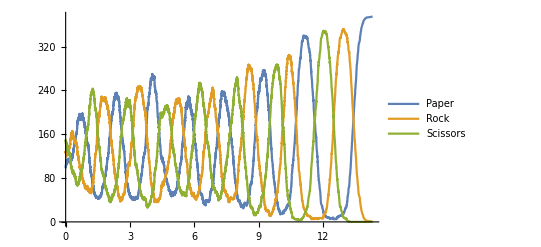

```mathematica
ListLinePlot[{DataTrace[history,P],DataTrace[history,R],DataTrace[history,S]},PlotLegends->{Paper,Rock,Scissors}]
```

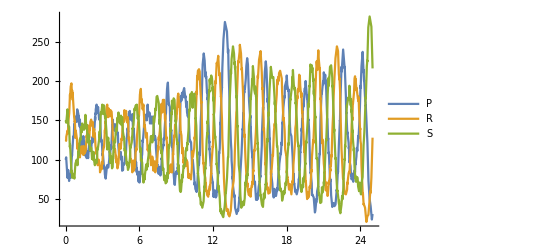

```mathematica
ListLinePlot[trajectory,PlotRange->{0,All},PlotLegends->SpeciesInRxnsys[crnCPP],MaxPlotPoints->500]
```

```mathematica
historySSA=FromTrajectorySSA[crnCPP,trajectory]; (* SSA simulation can be plotted in the same way as the original simulation, if you want. *)
```

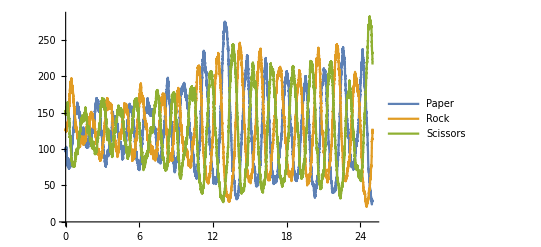

```mathematica
ListLinePlot[{DataTrace[historySSA,P],DataTrace[historySSA,R],DataTrace[historySSA,S]},PlotLegends->{Paper,Rock,Scissors}]
```

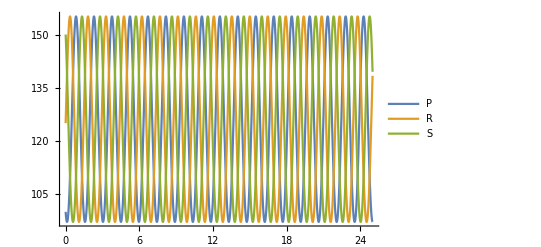

```mathematica
sol=SimulateRxnsys[Join[crnCPP,ToConcSSA[initialstateCPP]],25]; (* and now an ODE simulation too! *)
Plot[Evaluate[{P[t],R[t],S[t]}/.sol],{t,0,25},PlotRange->{0,All},PlotLegends->{P,R,S}]
```

We can see that for the rock-paper-scissors CRN, we are graphing on a time scale of 25 seconds and have between 0.5 and 1 oscillations per second for each species.  From our ODE simulation, we can see that this system will oscillate between 100 to 150 with all three species being offset equal amounts from each other. From the stochastic simulations, we see very similar pattern, but with the amplitudes increasing or decreasing. The asymptotic behavior of the stochastic systems seem to be the amplitudes of the oscillations increasing until one of the species hits 0; with only two species left, one more will hit zero and we will be left with a single species. The system goes to this state of a single species in a time scale of usually around tens of second (observed 10 - 75+ seconds, most often around 25 seconds).

```mathematica
RxnsToRxnls[{rxn[X+Y,Y+Y,1],rxn[Y+Z,Z+Z,1],rxn[Z+X,X+X,1]}]
```

{rxnl[{X,Y},{Y,Y},1],rxnl[{Y,Z},{Z,Z},1],rxnl[{X,Z},{X,X},1]}

```mathematica
SrinivasDSD=SrinivasCRN2DSD[{rxn[X+Y,Y+Y,1],rxn[Y+Z,Z+Z,1],rxn[Z+X,X+X,1]}] (* sort the species order *)
```

Mol[Rec[X] Toe[X[2]] Toe[Y[1]]]+Mol[Rec[X] Toe[X[2]] Toe[Z[1]]]+Mol[Rec[Y] Toe[Y[2]] Toe[Z[1]]]+Mol[Toe[X[1]] RecRxn2[3] Toe[X[1]]]+Mol[Toe[Y[1]] RecRxn2[1] Toe[Y[1]]]+Mol[Toe[Z[1]] RecRxn2[2] Toe[Z[1]]]+Mol[Rec[X] ( Toe[X[2]] ( Toe[Y[1]] ( + Rec[Y] ( Toe[Y[2]] ( RecRxn1[1] + ) ) ) ) ) Toe[X[1]]*]+Mol[Rec[X] ( Toe[X[2]] ( Toe[Z[1]] ( + Rec[Z] ( Toe[Z[2]] ( RecRxn1[3] + ) ) ) ) ) Toe[X[1]]*]+Mol[Rec[Y] ( Toe[Y[2]] ( Toe[Z[1]] ( + Rec[Z] ( Toe[Z[2]] ( RecRxn1[2] + ) ) ) ) ) Toe[Y[1]]*]+Mol[RecRxn1[1] ( Toe[Y[1]] ( Rec[Y] Toe[Y[2]] + RecRxn2[1] ( Toe[Y[1]] ( Rec[Y] Toe[Y[2]] + ) ) ) ) Toe[Y[2]]*]+Mol[RecRxn1[2] ( Toe[Z[1]] ( Rec[Z] Toe[Z[2]] + RecRxn2[2] ( Toe[Z[1]] ( Rec[Z] Toe[Z[2]] + ) ) ) ) Toe[Z[2]]*]+Mol[RecRxn1[3] ( Toe[X[1]] ( Rec[X] Toe[X[2]] + RecRxn2[3] ( Toe[X[1]] ( Rec[X] Toe[X[2]] + ) ) ) ) Toe[Z[2]]*]

```mathematica
SrinivasDSD=SrinivasCRN2DSD[{rxnl[{X,Y},{Y,Y},1],rxnl[{Y,Z},{Z,Z},1],rxnl[{Z,X},{X,X},1]}] (* preserve the species order *)
```

Mol[Rec[X] Toe[X[2]] Toe[Y[1]]]+Mol[Rec[Y] Toe[Y[2]] Toe[Z[1]]]+Mol[Rec[Z] Toe[Z[2]] Toe[X[1]]]+Mol[Toe[X[1]] RecRxn2[4] Toe[X[1]]]+Mol[Toe[Y[1]] RecRxn2[1] Toe[Y[1]]]+Mol[Toe[Z[1]] RecRxn2[2] Toe[Z[1]]]+Mol[Rec[X] ( Toe[X[2]] ( RecRxn1[4] + ) ) Toe[X[1]]* ( Toe[Z[2]]* ( Rec[Z]* ( Toe[Z[1]]* + ) ) )]+Mol[Rec[X] ( Toe[X[2]] ( Toe[Y[1]] ( + Rec[Y] ( Toe[Y[2]] ( RecRxn1[1] + ) ) ) ) ) Toe[X[1]]*]+Mol[Rec[Y] ( Toe[Y[2]] ( Toe[Z[1]] ( + Rec[Z] ( Toe[Z[2]] ( RecRxn1[2] + ) ) ) ) ) Toe[Y[1]]*]+Mol[RecRxn1[1] ( Toe[Y[1]] ( Rec[Y] Toe[Y[2]] + RecRxn2[1] ( Toe[Y[1]] ( Rec[Y] Toe[Y[2]] + ) ) ) ) Toe[Y[2]]*]+Mol[RecRxn1[2] ( Toe[Z[1]] ( Rec[Z] Toe[Z[2]] + RecRxn2[2] ( Toe[Z[1]] ( Rec[Z] Toe[Z[2]] + ) ) ) ) Toe[Z[2]]*]+Mol[RecRxn1[4] ( Toe[X[1]] ( Rec[X] Toe[X[2]] + RecRxn2[4] ( Toe[X[1]] ( Rec[X] Toe[X[2]] + ) ) ) ) Toe[X[2]]*]

```mathematica
{SriX,SriY,SriZ}=ToSimpleMol/@{HistorySignalMol[X],HistorySignalMol[Y],HistorySignalMol[Z]}
```

{SimpleMol[History Toe[X[1]] Rec[X] Toe[X[2]]],SimpleMol[History Toe[Y[1]] Rec[Y] Toe[Y[2]]],SimpleMol[History Toe[Z[1]] Rec[Z] Toe[Z[2]]]}

```mathematica
SimpleSriFuels=SrinivasDSD/.mol_Mol:>ToSimpleMol[mol]
```

SimpleMol[Rec[X] Toe[X[2]] Toe[Y[1]]]+SimpleMol[Rec[Y] Toe[Y[2]] Toe[Z[1]]]+SimpleMol[Rec[Z] Toe[Z[2]] Toe[X[1]]]+SimpleMol[Toe[X[1]] RecRxn2[4] Toe[X[1]]]+SimpleMol[Toe[Y[1]] RecRxn2[1] Toe[Y[1]]]+SimpleMol[Toe[Z[1]] RecRxn2[2] Toe[Z[1]]]+SimpleMol[Rec[X] ( Toe[X[2]] ( RecRxn1[4] + ) ) Toe[X[1]]* ( Toe[Z[2]]* ( Rec[Z]* ( Toe[Z[1]]* + ) ) )]+SimpleMol[Rec[X] ( Toe[X[2]] ( Toe[Y[1]] ( + Rec[Y] ( Toe[Y[2]] ( RecRxn1[1] + ) ) ) ) ) Toe[X[1]]*]+SimpleMol[Rec[Y] ( Toe[Y[2]] ( Toe[Z[1]] ( + Rec[Z] ( Toe[Z[2]] ( RecRxn1[2] + ) ) ) ) ) Toe[Y[1]]*]+SimpleMol[RecRxn1[1] ( Toe[Y[1]] ( Rec[Y] Toe[Y[2]] + RecRxn2[1] ( Toe[Y[1]] ( Rec[Y] Toe[Y[2]] + ) ) ) ) Toe[Y[2]]*]+SimpleMol[RecRxn1[2] ( Toe[Z[1]] ( Rec[Z] Toe[Z[2]] + RecRxn2[2] ( Toe[Z[1]] ( Rec[Z] Toe[Z[2]] + ) ) ) ) Toe[Z[2]]*]+SimpleMol[RecRxn1[4] ( Toe[X[1]] ( Rec[X] Toe[X[2]] + RecRxn2[4] ( Toe[X[1]] ( Rec[X] Toe[X[2]] + ) ) ) ) Toe[X[2]]*]

```mathematica
SimpleSriFuelsNoBack=Drop[SimpleSriFuels,3]
```

SimpleMol[Toe[X[1]] RecRxn2[4] Toe[X[1]]]+SimpleMol[Toe[Y[1]] RecRxn2[1] Toe[Y[1]]]+SimpleMol[Toe[Z[1]] RecRxn2[2] Toe[Z[1]]]+SimpleMol[Rec[X] ( Toe[X[2]] ( RecRxn1[4] + ) ) Toe[X[1]]* ( Toe[Z[2]]* ( Rec[Z]* ( Toe[Z[1]]* + ) ) )]+SimpleMol[Rec[X] ( Toe[X[2]] ( Toe[Y[1]] ( + Rec[Y] ( Toe[Y[2]] ( RecRxn1[1] + ) ) ) ) ) Toe[X[1]]*]+SimpleMol[Rec[Y] ( Toe[Y[2]] ( Toe[Z[1]] ( + Rec[Z] ( Toe[Z[2]] ( RecRxn1[2] + ) ) ) ) ) Toe[Y[1]]*]+SimpleMol[RecRxn1[1] ( Toe[Y[1]] ( Rec[Y] Toe[Y[2]] + RecRxn2[1] ( Toe[Y[1]] ( Rec[Y] Toe[Y[2]] + ) ) ) ) Toe[Y[2]]*]+SimpleMol[RecRxn1[2] ( Toe[Z[1]] ( Rec[Z] Toe[Z[2]] + RecRxn2[2] ( Toe[Z[1]] ( Rec[Z] Toe[Z[2]] + ) ) ) ) Toe[Z[2]]*]+SimpleMol[RecRxn1[4] ( Toe[X[1]] ( Rec[X] Toe[X[2]] + RecRxn2[4] ( Toe[X[1]] ( Rec[X] Toe[X[2]] + ) ) ) ) Toe[X[2]]*]

```mathematica
Timing[SimpleSriRPS=SimpleEnumerateDSD[SpeciesInSum[SrinivasDSD+HistorySignalMol[X]+HistorySignalMol[Y]+HistorySignalMol[Z]]];]
```

0 reactions and 0 species enumerated, 15 yet to go.

6 reactions and 15 species enumerated, 3 yet to go.

12 reactions and 18 species enumerated, 6 yet to go.

15 reactions and 24 species enumerated, 6 yet to go.

30 reactions and 30 species enumerated, 12 yet to go.

51 reactions and 42 species enumerated, 15 yet to go.

63 reactions and 57 species enumerated, 9 yet to go.

63 reactions and 66 species enumerated when all is said and done.

{31.8438,Null}

```mathematica
SriXvariants=Select[SpeciesInRxnsys[SimpleSriRPS],StringMatchQ[ToString[#],___~~"Toe[X[1]] Rec[X] Toe[X[2]]]"]&];
SriYvariants=Select[SpeciesInRxnsys[SimpleSriRPS],StringMatchQ[ToString[#],___~~"Toe[Y[1]] Rec[Y] Toe[Y[2]]]"]&];
SriZvariants=Select[SpeciesInRxnsys[SimpleSriRPS],StringMatchQ[ToString[#],___~~"Toe[Z[1]] Rec[Z] Toe[Z[2]]]"]&];
```

```mathematica
SriZvariants
```

{SimpleMol[History Toe[Z[1]] Rec[Z] Toe[Z[2]]],SimpleMol[RecRxn1[2] Toe[Z[1]] Rec[Z] Toe[Z[2]]],SimpleMol[RecRxn2[2] Toe[Z[1]] Rec[Z] Toe[Z[2]]]}

```mathematica
Timing[{trajectory,species2numbers}=SimulateReactionSchemaSSA[DSDschemata,1000SimpleSriFuelsNoBack+10SriX+20SriY+20SriZ,300000,CRN->SimpleSriRPS,Trajectory->True];Length[trajectory["Times"]]]
```

{2.71875,140577}

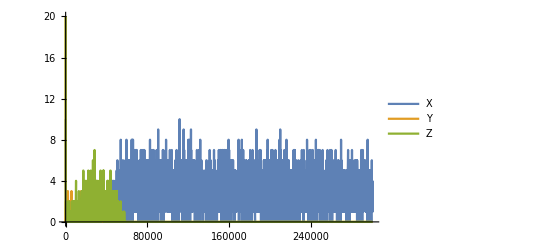

```mathematica
With[{trajlists=PlotFormat[trajectory,5000],tmax=300000 },
ListLinePlot[{SumVariants[trajlists,SriXvariants,species2numbers],SumVariants[trajlists,SriYvariants,species2numbers],SumVariants[trajlists,SriZvariants,species2numbers]},PlotLegends->{"X","Y","Z"},PlotRange->{{0,tmax},{0,All}}]]
```

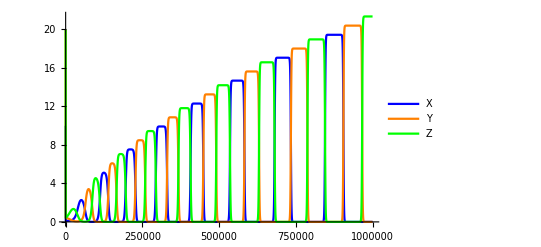

```mathematica
With[{tmax=1000000},
sol=SimulateReactionSchemaBulk[DSDschemata,1000SimpleSriFuelsNoBack+10SriX+20SriY+20SriZ,tmax,CRN->SimpleSriRPS];
Plot[Evaluate[{Plus@@(#[t]&/@SriXvariants),Plus@@(#[t]&/@SriYvariants),Plus@@(#[t]&/@SriZvariants)}/.sol],{t,0,tmax},PlotRange->{0,All},
PlotStyle->{{Blue},{Orange},{Green}},PlotLegends->{"X","Y","Z"}]
]
```

```mathematica
50000/60/60 hours//N
```

13.8889 hours

We can see that for the rock-paper-scissors DSD, we are graphing on a time scale of 27-277 hours and has an oscillation once per 17ish hours for each species.  From the stochastic simulations, see some oscillation at the beginning, but it reaches the asymptotic behavior of increasing until two species go to zero around 14 hours. From our simulations, we see that they seem to oscillate around the 0-5 range. In bulk simulation, the size of the oscillations in this system increases.

Both the CRN and the DSD stochastic simulations have similar general behavior with some oscillations before two species go to zero. For the non-stochastic simulations, both never have species that go to zero, but for the CRN the oscillations stay constant and the DSD oscillations increase. The time scale is also very different between the two with a scale of tens of seconds for the CRN and a scale of tens of hours for the DSD.

(b) Explain why the simplified DSD behaves as it does, in particular paying attention to the roles played by the changing concentrations of the fuel molecules (gates, backward strands, helper strands, wastes).

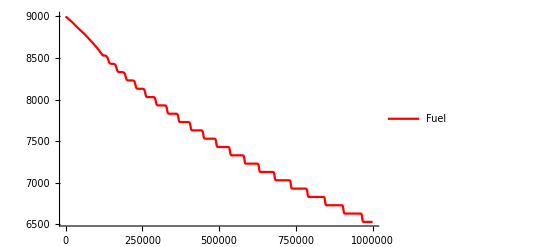

```mathematica
With[{tmax=1000000},
sol=SimulateReactionSchemaBulk[DSDschemata,1000SimpleSriFuelsNoBack+10SriX+20SriY+20SriZ,tmax,CRN->SimpleSriRPS];
Plot[Evaluate[{Plus@@(#[t]&/@SimpleSriFuels)}/.sol],{t,0,tmax},PlotRange->{0,All},
PlotStyle->{{Red}},PlotLegends->{"Fuel"}]
]
```

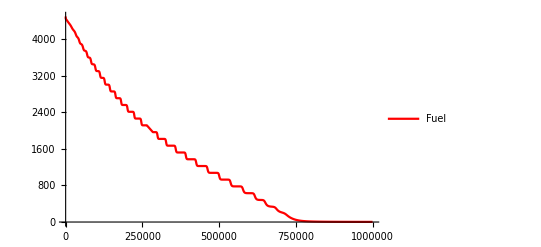

```mathematica
With[{tmax=1000000},
sol=SimulateReactionSchemaBulk[DSDschemata,500SimpleSriFuelsNoBack+10SriX+20SriY+20SriZ,tmax,CRN->SimpleSriRPS];
Plot[Evaluate[{Plus@@(#[t]&/@SimpleSriFuelsNoBack)}/.sol],{t,0,tmax},PlotRange->{0,All},
PlotStyle->{{Red}},PlotLegends->{"Fuel"}]
]
```

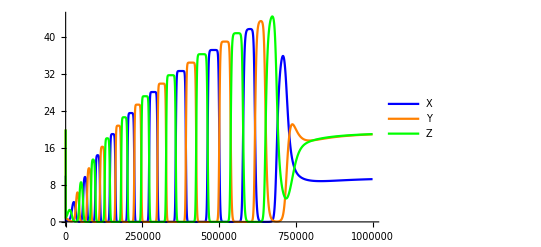

```mathematica
With[{tmax=1000000},
sol=SimulateReactionSchemaBulk[DSDschemata,500SimpleSriFuelsNoBack+10SriX+20SriY+20SriZ,tmax,CRN->SimpleSriRPS];
Plot[Evaluate[{Plus@@(#[t]&/@SriXvariants),Plus@@(#[t]&/@SriYvariants),Plus@@(#[t]&/@SriZvariants)}/.sol],{t,0,tmax},PlotRange->{0,All},
PlotStyle->{{Blue},{Orange},{Green}},PlotLegends->{"X","Y","Z"}]
]
```

The DSD increases in concentration in the bulk simulations because new X, Y, Z molecules are added from the fuel molecules. We can see that as the amount of fuel decreases the amplitude of the oscillations increases, and once the fuel runs out the reactions stop. Since the bulk reactions don’t have randomness unlike the stochastic simulations, all of the molecules will be used so the molecules added from the fuel will cause the oscillations to increase in amplitude.

(c) Demonstrate sustained operation of the DSD oscillator when the fuel molecules are chemostatted.  You may of course use thee code in the notebook for chemostatting.  The challenge here is to determine suitable concentrations for chemostatting each fuel species.

```mathematica
SpeciesInSum[SimpleSriFuelsNoBack]
```

{SimpleMol[Toe[X[1]] RecRxn2[4] Toe[X[1]]],SimpleMol[Toe[Y[1]] RecRxn2[1] Toe[Y[1]]],SimpleMol[Toe[Z[1]] RecRxn2[2] Toe[Z[1]]],SimpleMol[Rec[X] ( Toe[X[2]] ( RecRxn1[4] + ) ) Toe[X[1]]* ( Toe[Z[2]]* ( Rec[Z]* ( Toe[Z[1]]* + ) ) )],SimpleMol[Rec[X] ( Toe[X[2]] ( Toe[Y[1]] ( + Rec[Y] ( Toe[Y[2]] ( RecRxn1[1] + ) ) ) ) ) Toe[X[1]]*],SimpleMol[Rec[Y] ( Toe[Y[2]] ( Toe[Z[1]] ( + Rec[Z] ( Toe[Z[2]] ( RecRxn1[2] + ) ) ) ) ) Toe[Y[1]]*],SimpleMol[RecRxn1[1] ( Toe[Y[1]] ( Rec[Y] Toe[Y[2]] + RecRxn2[1] ( Toe[Y[1]] ( Rec[Y] Toe[Y[2]] + ) ) ) ) Toe[Y[2]]*],SimpleMol[RecRxn1[2] ( Toe[Z[1]] ( Rec[Z] Toe[Z[2]] + RecRxn2[2] ( Toe[Z[1]] ( Rec[Z] Toe[Z[2]] + ) ) ) ) Toe[Z[2]]*],SimpleMol[RecRxn1[4] ( Toe[X[1]] ( Rec[X] Toe[X[2]] + RecRxn2[4] ( Toe[X[1]] ( Rec[X] Toe[X[2]] + ) ) ) ) Toe[X[2]]*]}

```mathematica
SpeciesInRxnsys[SimpleSriRPS];
```

We can chemostat all of the fuel species to be 0, and there are no oscillations as we would expect.

```mathematica
nofuels=BulkChemostat[SimpleSriRPS,{conc[SpeciesInSum[SimpleSriFuelsNoBack][[1]],0],conc[SpeciesInSum[SimpleSriFuelsNoBack][[2]],0],conc[SpeciesInSum[SimpleSriFuelsNoBack][[3]],0],conc[SpeciesInSum[SimpleSriFuelsNoBack][[4]],0],conc[SpeciesInSum[SimpleSriFuelsNoBack][[5]],0],conc[SpeciesInSum[SimpleSriFuelsNoBack][[6]],0],conc[SpeciesInSum[SimpleSriFuelsNoBack][[7]],0],conc[SpeciesInSum[SimpleSriFuelsNoBack][[8]],0],conc[SpeciesInSum[SimpleSriFuelsNoBack][[9]],0]}];
```

```mathematica
Length[SimpleSriRPS]
```

54

```mathematica
Length[test]
```

0

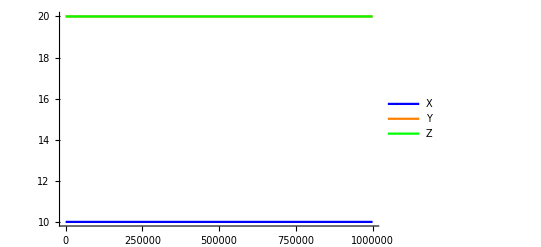

```mathematica
With[{tmax=1000000},
sol=SimulateReactionSchemaBulk[DSDschemata,10SriX+20SriY+20SriZ,tmax,CRN->nofuels];
Plot[Evaluate[{Plus@@(#[t]&/@SriXvariants),Plus@@(#[t]&/@SriYvariants),Plus@@(#[t]&/@SriZvariants)}/.sol],{t,0,tmax},PlotRange->{0,All},
PlotStyle->{{Blue},{Orange},{Green}},PlotLegends->{"X","Y","Z"}]
]
```

We can chemostat all of the fuel species to be 1, and there are very small and slow oscillations because there is very little fuel to facilitate reactions.

```mathematica
fuel1=BulkChemostat[SimpleSriRPS,{conc[SpeciesInSum[SimpleSriFuelsNoBack][[1]],1],conc[SpeciesInSum[SimpleSriFuelsNoBack][[2]],1],conc[SpeciesInSum[SimpleSriFuelsNoBack][[3]],1],conc[SpeciesInSum[SimpleSriFuelsNoBack][[4]],1],conc[SpeciesInSum[SimpleSriFuelsNoBack][[5]],1],conc[SpeciesInSum[SimpleSriFuelsNoBack][[6]],1],conc[SpeciesInSum[SimpleSriFuelsNoBack][[7]],1],conc[SpeciesInSum[SimpleSriFuelsNoBack][[8]],1],conc[SpeciesInSum[SimpleSriFuelsNoBack][[9]],1]}];
```

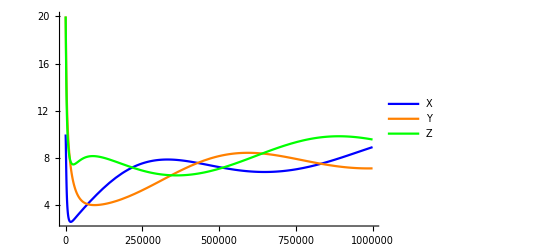

```mathematica
With[{tmax=1000000},
sol=SimulateReactionSchemaBulk[DSDschemata,10SriX+20SriY+20SriZ,tmax,CRN->fuel1];
Plot[Evaluate[{Plus@@(#[t]&/@SriXvariants),Plus@@(#[t]&/@SriYvariants),Plus@@(#[t]&/@SriZvariants)}/.sol],{t,0,tmax},PlotRange->{0,All},
PlotStyle->{{Blue},{Orange},{Green}},PlotLegends->{"X","Y","Z"}]
]
```

We can chemostat all of the fuel species to be 1000, and we get a bulk simulation that looks nearly identical to our non-chemostatted bulk simulation. We also see that the stochastic simulations are very similar to that of part a.

```mathematica
statted=BulkChemostat[SimpleSriRPS,{conc[SpeciesInSum[SimpleSriFuelsNoBack][[1]],1000],conc[SpeciesInSum[SimpleSriFuelsNoBack][[2]],1000],conc[SpeciesInSum[SimpleSriFuelsNoBack][[3]],1000],conc[SpeciesInSum[SimpleSriFuelsNoBack][[4]],1000],conc[SpeciesInSum[SimpleSriFuelsNoBack][[5]],1000],conc[SpeciesInSum[SimpleSriFuelsNoBack][[6]],1000],conc[SpeciesInSum[SimpleSriFuelsNoBack][[7]],1000],conc[SpeciesInSum[SimpleSriFuelsNoBack][[8]],1000],conc[SpeciesInSum[SimpleSriFuelsNoBack][[9]],1000]}];
```

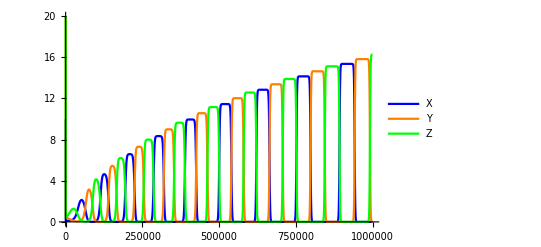

```mathematica
With[{tmax=1000000},
sol=SimulateReactionSchemaBulk[DSDschemata,10SriX+20SriY+20SriZ,tmax,CRN->statted];
Plot[Evaluate[{Plus@@(#[t]&/@SriXvariants),Plus@@(#[t]&/@SriYvariants),Plus@@(#[t]&/@SriZvariants)}/.sol],{t,0,tmax},PlotRange->{0,All},
PlotStyle->{{Blue},{Orange},{Green}},PlotLegends->{"X","Y","Z"}]
]
```

```mathematica
With[{tmax=1000000},
sol=SimulateReactionSchemaBulk[DSDschemata,1000SimpleSriFuelsNoBack+10SriX+20SriY+20SriZ,tmax,CRN->SimpleSriRPS];
Plot[Evaluate[{Plus@@(#[t]&/@SriXvariants),Plus@@(#[t]&/@SriYvariants),Plus@@(#[t]&/@SriZvariants)}/.sol],{t,0,tmax},PlotRange->{0,All},
PlotStyle->{{Blue},{Orange},{Green}},PlotLegends->{"X","Y","Z"}]
]
```

-Graphics-

```mathematica
Timing[{trajectory,species2numbers}=SimulateReactionSchemaSSA[DSDschemata,10SriX+20SriY+20SriZ,300000,CRN->statted,Trajectory->True];Length[trajectory["Times"]]]
```

{2.32813,157211}

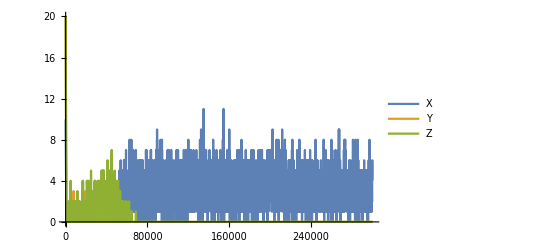

```mathematica
With[{trajlists=PlotFormat[trajectory,5000],tmax=300000 },
ListLinePlot[{SumVariants[trajlists,SriXvariants,species2numbers],SumVariants[trajlists,SriYvariants,species2numbers],SumVariants[trajlists,SriZvariants,species2numbers]},PlotLegends->{"X","Y","Z"},PlotRange->{{0,tmax},{0,All}}]]
```

When we chemostat all of the fuel species to be 10000, we get some weird activity of very small, slow oscilations.

```mathematica
largeConc=BulkChemostat[SimpleSriRPS,{conc[SpeciesInSum[SimpleSriFuelsNoBack][[1]],10000],conc[SpeciesInSum[SimpleSriFuelsNoBack][[2]],10000],conc[SpeciesInSum[SimpleSriFuelsNoBack][[3]],10000],conc[SpeciesInSum[SimpleSriFuelsNoBack][[4]],10000],conc[SpeciesInSum[SimpleSriFuelsNoBack][[5]],10000],conc[SpeciesInSum[SimpleSriFuelsNoBack][[6]],10000],conc[SpeciesInSum[SimpleSriFuelsNoBack][[7]],10000],conc[SpeciesInSum[SimpleSriFuelsNoBack][[8]],10000],conc[SpeciesInSum[SimpleSriFuelsNoBack][[9]],10000]}];
```

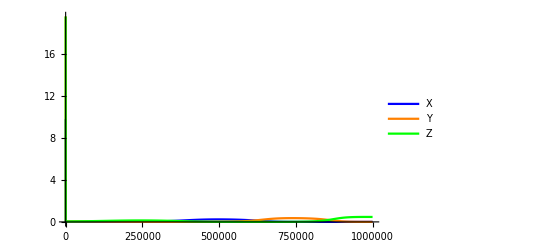

```mathematica
With[{tmax=1000000},
sol=SimulateReactionSchemaBulk[DSDschemata,10SriX+20SriY+20SriZ,tmax,CRN->largeConc];
Plot[Evaluate[{Plus@@(#[t]&/@SriXvariants),Plus@@(#[t]&/@SriYvariants),Plus@@(#[t]&/@SriZvariants)}/.sol],{t,0,tmax},PlotRange->{0,All},
PlotStyle->{{Blue},{Orange},{Green}},PlotLegends->{"X","Y","Z"}]
]
```